# Grammar-based genetic programming

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```

## Grammar definition and parsing

### Trading grammar description and possible terminals set

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];
TerminalsPrettify[terminalSet_]:=Block[{gathered},
gathered = GatherBy[terminalSet/.Term[l_,v_]:>{l,v},First];
Column@Map[Style[#[[1,1]],Italic]->#[[All,2]]&,gathered]
];

grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["priceQuant"],NonTerm["priceQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["priceQuant"]["Value"],NonTerm["priceQuant"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["volumeQuant"],NonTerm["volumeQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["volumeQuant"]["Value"],NonTerm["volumeQuant"]["Value"]]|>,

<|"From"->"priceQuant","To"->{Term["factor"],NonTerm["priceExpression"]},
"Value"->Times[Term["factor"]["Value"],NonTerm["priceExpression"]["Value"]]|>,

<|"From"->"priceQuant","To"->{NonTerm["priceExpression"]},
"Value"->NonTerm["priceExpression"]["Value"]|>,

<|"From"->"volumeQuant","To"->{Term["volumeValue"]},
"Value"->Term["volumeValue"]["Value"]|>,

<|"From"->"volumeQuant","To"->{NonTerm["volumeExpression"]},
"Value"->NonTerm["volumeExpression"]["Value"]|>,

<|"From"->"priceExpression","To"->{Term["techInd"],Term["observable"],Term["window"]},
"Value"->Term["techInd"]["Value"][Term["observable"]["Value"],Term["window"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["lag"],Term["observable"]},
"Value"->Prev[Term["observable"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["observable"]},
"Value"->Term["observable"]["Value"]|>,

<|"From"->"volumeExpression","To"->{Term["lag"],Term["volume"]},
"Value"->Prev[Term["volume"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"volumeExpression","To"->{Term["volume"]},
"Value"->Term["volume"]["Value"]|>
};
terminalSet = {
Term["logicOp","And"],Term["logicOp","Or"],Term["logicOp","Xor"],
Term["numOp","Greater"],Term["numOp","GreaterEqual"],Term["numOp","Less"],Term["numOp","LessEqual"],
Term["observable","Open"],Term["observable","Low"],Term["observable","High"],Term["observable","Close"],
Term["lag","1"],Term["lag","5"],Term["lag","10"],Term["lag","20"],
Term["window","2"],Term["window","5"],Term["window","10"],Term["window","15"],Term["window","20"],
Term["factor","0.5"],Term["factor","0.7"],Term["factor","0.9"],Term["factor","1.1"],Term["factor","1.3"],Term["factor","1.5"],Term["factor","2.0"],
Term["techInd","SMA"],Term["techInd","EMA"],
Term["not","Not"],Term["volume","Volume"],
Term["volumeValue","1000"],Term["volumeValue","5000"],Term["volumeValue","10000"],Term["volumeValue","50000"],Term["volumeValue","100000"],Term["volumeValue","500000"]
};
```

```mathematica
GrammarPrettify[grammar]
```

cond→{logicOp,cond,cond}
cond→{not,cond}
cond→{numOp,priceQuant,priceQuant}
cond→{numOp,volumeQuant,volumeQuant}
priceQuant→{factor,priceExpression}
priceQuant→{priceExpression}
volumeQuant→{volumeValue}
volumeQuant→{volumeExpression}
priceExpression→{techInd,observable,window}
priceExpression→{lag,observable}
priceExpression→{observable}
volumeExpression→{lag,volume}
volumeExpression→{volume}

```mathematica
TerminalsPrettify[terminalSet]
```

logicOp→{And,Or,Xor}
numOp→{Greater,GreaterEqual,Less,LessEqual}
observable→{Open,Low,High,Close}
lag→{1,5,10,25,50}
window→{10,20,30,40,50}
factor→{0.5,0.7,0.9,1.1,1.3,1.5,2.0}
techInd→{SMA,EMA}
not→{Not}
volume→{Volume}
volumeValue→{1000,5000,10000,50000,100000,500000}

```mathematica
GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle,ImageSize->800]
];
```

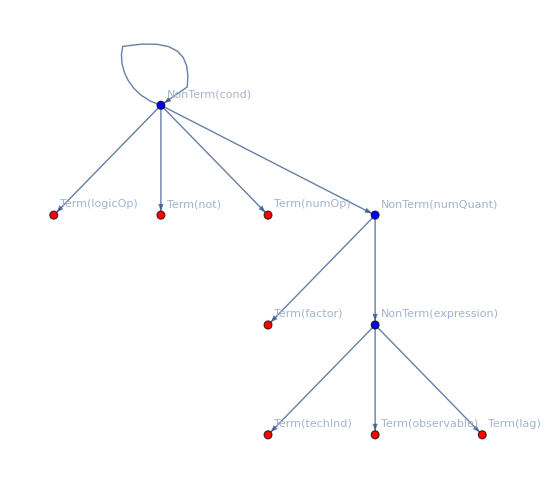

```mathematica
GrammarGraph[grammar]
```

### Expression tree synthesization

Separate head from arguments

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]==3]:=Prepend[Level[expr,{1}],Head[expr]];
```

```mathematica
GetComponents[Less["Close",Prev[3,"Open"]]]
```

{Less,Close,Prev[3,Open]}

Rebuild expression from components

```mathematica
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];
```

```mathematica
ExprFromComponents[{Less,"Close",Prev[3,"Open"]}] // FullForm
```

Less["Close",Prev[3,"Open"]]

Find the positions of values to be synthesized on the synthesizations list

```mathematica
GetValue[treeSymbol_,grammar_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found],
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
synthValue = GetValue[NonTerm["expression",8],grammar]
```

Term[observable][Value]

```mathematica
MatchPositions[GetComponents[synthValue],{Term["observable"]["Value"],Term["numOp"]["Value"],Term["logicOp"]["Value"]}]
```

{{1}}

Synthesize the value of the current components from the list of synthValues.

```mathematica
Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];
ExprFromComponents@tmpExprComponents
];
```

```mathematica
GetComponents[synthValue]
```

{Term[observable][Value]}

```mathematica
Synthesize[
GetComponents[synthValue],
Extract[{Term["observable"]["Value"]->"High",Term["numOp"]["Value"]->"Greater",Term["logicOp"]["Value"]->"And"},{{1}}]
]
```

High

Synthesize terminals and nonterminals.

```mathematica
SynthesizeNonTerm[treeSymbol_,grammar_,synthesizations_]:=Block[{val,components,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol,grammar];
components = GetComponents[val];
matchPos = MatchPositions[components,synthesizations[[All,1]]];
eval = Synthesize[components,Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

Complete tree synthesization.

```mathematica
SynthesizeTree[graph_,labels_,grammar_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,grammar,synthesized]];
,
{s,labeledDFS}
];

ToExpression@ToString@Return[synthesized[[1,-1]]] /.{Open->"Open",High->"High",Low->"Low",Close->"Close",Volume->"Volume"}
];

FormatStep[step_]:=Column[{
Style["Next symbol:",Bold],
step[[1]],
Style["Next production:",Bold],
step[[2]],
Style["Synthesized:",Bold],
step[[3]],
Style["Tree:",Bold],
step[[4]]
}];
ViewSynthesization[graph_,labels_,grammar_]:=DynamicModule[{depthFirstScan,labeledDFS,symbolType,synthesized,synthesis,formattedSynthesis},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
synthesis = First@Last@Reap@Do[
symbolType = Head[labeledDFS[[i]]];
If[symbolType === Term,synthesized = SynthesizeTerm[labeledDFS[[i]],synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[labeledDFS[[i]],grammar,synthesized]];

If[i!=Length[depthFirstScan],
Sow[{labeledDFS[[i+1]],GetValue[labeledDFS[[i+1]],grammar],synthesized,VertexDelete[graph,Take[depthFirstScan,{1,i}]]}],
Sow[{None,None,synthesized,VertexDelete[graph,Take[depthFirstScan,{1,i}]]}]
];
,
{i,1,Length[depthFirstScan],1}
];

formattedSynthesis = Map[FormatStep,synthesis];

Manipulate[formattedSynthesis[[i]],{i,1,Length[formattedSynthesis],1},SaveDefinitions->True]
];
```

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet,100];
ViewSynthesization[g,l,grammar]
```

## Operations on trees

Tree manipulations operations.

```mathematica
RestartLabelsAt[graph_,labels_,startNum_ : 1]:=Block[{replaceRules,newEdges,newLabels},
replaceRules = Thread[VertexList[graph]->Range[startNum,startNum+Length[VertexList[graph]]-1]];
newEdges = EdgeList[graph]/.replaceRules;
newLabels = MapAt[#/.replaceRules&,labels,{All,1}];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->newLabels,ImageSize->500],newLabels}
];

InsertSubtree[graph_,labels_,subtree_,sublabels_]:=Block[{missingVertexes,edges,missing,splitPos,left,right,middleRules,formattedSubtreeRoot,remaining,rightRules,newLeftGraph,newMiddleGraph,newRightGraph,insertLabels,incompleteLabels,newEdges,newLabels,newRootForSub,newRightLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missingVertexes = Complement[Range[Max[edges]],edges];
If[missingVertexes ≠ {},
missing =  First@missingVertexes;
splitPos = First@FirstPosition[EdgeList[graph],_->Empty];
{left,right} = TakeDrop[EdgeList[graph],splitPos];

middleRules = Thread[VertexList[subtree]->(VertexList[subtree]+missing-1)];
newMiddleGraph = EdgeList[subtree]/.middleRules;
formattedSubtreeRoot = 1 /.middleRules;

remaining = Complement[VertexList[right],VertexList[left]];
rightRules = Thread[remaining->(remaining+Max[VertexList[newMiddleGraph]]-Min[remaining]+1)];

newLeftGraph = left/.Empty->formattedSubtreeRoot;
newRightGraph = right /.rightRules;
insertLabels = MapAt[#/.middleRules&,sublabels,{All,1}];
incompleteLabels = MapAt[#/.rightRules&,labels,{All,1}];

newEdges = Join[newLeftGraph,newMiddleGraph,newRightGraph];
newLabels = SortBy[Join[incompleteLabels,insertLabels],First];

,

newRootForSub = Max[DeleteCases[VertexList[graph],Empty]]+1;
{newRightGraph,newRightLabels} = RestartLabelsAt[subtree,sublabels,newRootForSub];
newEdges = Join[EdgeList[graph]/.Empty->newRootForSub,EdgeList[newRightGraph]];
newLabels = Join[labels,newRightLabels];
];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
```

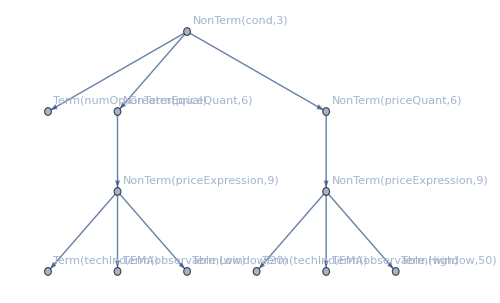
```mathematica
{g1,labels1} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","GreaterEqual"],3->NonTerm["priceQuant",6],4->NonTerm["priceExpression",9],5->Term["techInd","EMA"],6->Term["observable","Low"],7->Term["window","20"],8->NonTerm["priceQuant",6],9->NonTerm["priceExpression",9],10->Term["techInd","EMA"],11->Term["observable","High"],12->Term["window","50"]}};
```

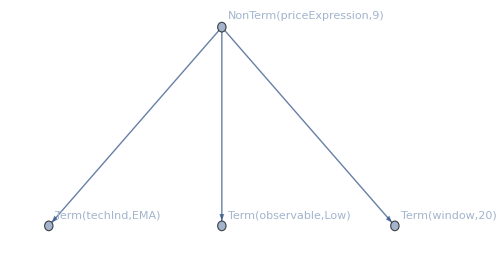
{-Graphics-,{1→NonTerm[priceExpression,9],2→Term[techInd,EMA],3→Term[observable,Low],4→Term[window,20]}}

```mathematica
subtree1 = Apply[RestartLabelsAt,Subtree[g1,labels1,4]]
```

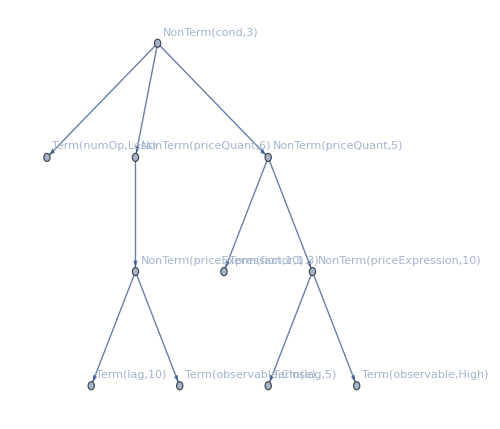
```mathematica
{g2,labels2} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","Less"],3->NonTerm["priceQuant",6],4->NonTerm["priceExpression",10],5->Term["lag","10"],6->Term["observable","Close"],7->NonTerm["priceQuant",5],8->Term["factor","1.3"],9->NonTerm["priceExpression",10],10->Term["lag","5"],11->Term["observable","High"]}};
```

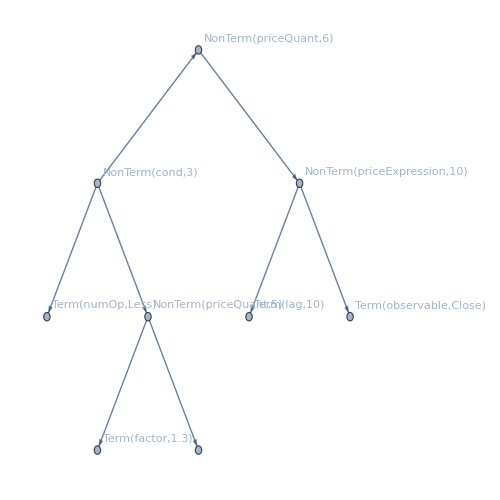
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,5],8→Term[factor,1.3]}}

```mathematica
cropped2 = DeleteSubtree[g2,labels2,9]
```

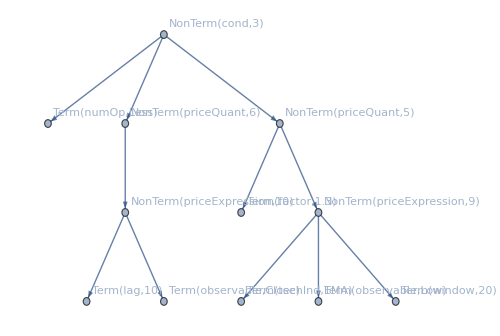
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,5],8→Term[factor,1.3],9→NonTerm[priceExpression,9],10→Term[techInd,EMA],11→Term[observable,Low],12→Term[window,20]}}

```mathematica
inserted = InsertSubtree[First[cropped2],Last[cropped2],First[subtree1],Last[subtree1]]
```

```mathematica
SynthesizeTree[First[inserted],Last[inserted],grammar] // FullForm
```

Less[Prev["Close",10],Times[1.3,EMA["Low",20]]]

## Crossover

Crossover operator that selects NonTerms that are common in both parents and swaps them.

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{nonterms1,nonterms2,commonNonTerms,matchsIn1,vertex1,vertex1NonTerm,vertex2,cropped,sub},
nonterms1 = Cases[labels1[[All,2]],_NonTerm];
nonterms2 = Cases[labels2[[All,2]],_NonTerm];
commonNonTerms = Intersection[nonterms1,nonterms2];

matchsIn1 = Cases[labels1,HoldPattern[v_->l_/;MemberQ[commonNonTerms,l]]:>{v,l}];
If[Length[matchsIn1]<2,Return[RandomChoice[{{graph1,labels1},{graph2,labels2}}]]];

{vertex1,vertex1NonTerm} = RandomChoice[Drop[matchsIn1,1]];
vertex2 = RandomChoice[Cases[labels2,HoldPattern[v_->l_/;l==vertex1NonTerm]:>v]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Apply[RestartLabelsAt,Subtree[graph2,labels2,vertex2]];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]]
];
CoupleCrossover[ind1_,ind2_]:=Block[{childGenome,childScore},
childGenome = Crossover[First[ind1["Genome"]],Last[ind1["Genome"]],First[ind2["Genome"]],Last[ind2["Genome"]]];
childScore = (2*Mean[{ind1["Score"],ind2["Score"]}])/3;
<|"Genome"->childGenome,"Score"->childScore|>
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[CoupleCrossover,#]&,parts],childrenPerCouple]]
];
```

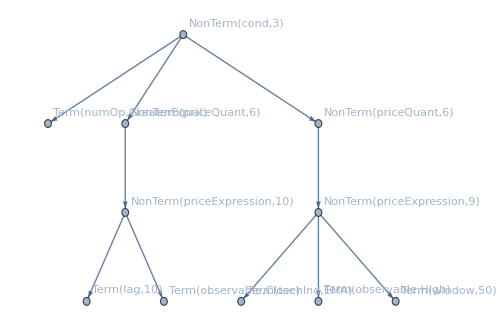
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,GreaterEqual],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,6],8→NonTerm[priceExpression,9],9→Term[techInd,EMA],10→Term[observable,High],11→Term[window,50]}}

```mathematica
{crossoverTree,crossoverLabels} = Crossover[g1,labels1,g2,labels2]
```

```mathematica
SynthesizeTree[crossoverTree,crossoverLabels,grammar]// FullForm
```

GreaterEqual[Prev["Close",10],EMA["High",50]]

## Mutation

```mathematica
TreeMutation[graph_,labels_]:=Crossover[graph,labels,graph,labels];
TerminalMutation[labels_,terminalSet_]:=Block[{choice,type,newTerm,availableTerms},
choice = RandomChoice[Cases[labels,HoldPattern[_->_Term]]];
type = First[Level[Last[choice],{1}]];
availableTerms = Complement[Cases[terminalSet,Term[type,_]],{Last[choice]}];

If[availableTerms ≠ {},
newTerm = RandomChoice[availableTerms];
ReplacePart[labels,First[choice]->(First[choice]->newTerm)]
,
labels
]
];
Mutation[graph_,labels_,terminalSet_]:=Block[{mutatedSymbols},
If[RandomReal[]≥0.5,
TreeMutation[graph,labels],
mutatedSymbols = TerminalMutation[labels,terminalSet];
{Graph[EdgeList[graph],VertexLabels->mutatedSymbols,ImageSize->500],mutatedSymbols}
]
];
MutateIndividual[ind_]:=<|"Genome"->Mutation[First[ind["Genome"]],Last[ind["Genome"]],terminalSet],"Score"->ind["Score"]|>;
PopulationMutate[population_,probability_,terminalSet_]:=Map[If[RandomReal[]≤probability,MutateIndividual[#],#]&,population];
```

```mathematica
{mutatedTree,mutatedLabels} = Mutation[g1,labels1,terminalSet]
```

{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,GreaterEqual],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,9],5→Term[techInd,EMA],6→Term[observable,Low],7→Term[window,20],8→NonTerm[priceQuant,6],9→NonTerm[priceExpression,9],10→Term[techInd,EMA],11→Term[observable,High],12→Term[window,50]}}

```mathematica
SynthesizeTree[mutatedTree,mutatedLabels,grammar]
```

EMA[Low,20]≥EMA[High,50]

## Fitness function

### Database creation

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders]
```

{2020-01-20,2020-01-21,2020-01-22,2020-01-23,2020-01-24,2020-01-27,2020-01-28,2020-01-29,2020-01-30,2020-01-31,2020-02-04,2020-02-05,2020-02-06,2020-02-07,2020-02-10,2020-02-11,2020-02-12,2020-02-13,2020-02-14,2020-02-17,2020-02-18,2020-02-19}

```mathematica
{trainingDates,validationDates} = TakeDrop[dates,Ceiling[0.8Length[dates]]];
```

```mathematica
stockPaths = FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",First[dates]}]];
stocks = Map[FileBaseName,stockPaths]
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
AdaptativeMovingAverage[maFunc_,list_,r_]:=Join[Table[First@maFunc[Take[list,n],n],{n,1,r-1}],maFunc[list,r]];
LaggedList[list_,lag_]:=Join[ConstantArray[First[list],lag],Drop[list,-lag]];

BuildDerivatives[dataset_]:=Block[{keys,windows,obsWindowTuples,sma,ema,lags,obsLagTuples,prev,derivatives,derivativesData},
keys = Keys[First[dataset]];
windows = Cases[terminalSet,Term["window",l_]:>ToExpression[l]];
obsWindowTuples = Tuples[{keys,windows}];
lags = Cases[terminalSet,Term["lag",l_]:>ToExpression[l]];
obsLagTuples = Tuples[{keys,lags}];

sma =Map[Apply[SMA,#]->AdaptativeMovingAverage[MovingAverage,dataset[[All,First[#]]],Last[#]]&,obsWindowTuples];
ema =Map[Apply[EMA,#]->ExponentialMovingAverage[dataset[[All,First[#]]],Last[#]/50]&,obsWindowTuples];
prev = Map[Apply[Prev,#]->LaggedList[dataset[[All,First[#]]],Last[#]]&,obsLagTuples];
derivatives = Map[Thread,Join[sma,ema,prev]];
derivativesData = Map[Association,Transpose[derivatives]];

MapThread[Join,{derivativesData,dataset}]

];
```

```mathematica
CreateTick[{open_,high_,low_,close_,volume_}]:=<|"Open"->open,"High"->high,"Low"->low,"Close"->close,"Volume"->volume|>;
CreateTickDatabase[date_,stock_]:=Block[{path,dataset},
path = FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",date}];
dataset = DeleteCases[Import[FileNameJoin[{path,StringJoin[stock,".csv"]}]],{_,"","","","",""}];

BuildDerivatives@Map[CreateTick[Drop[#,1]]&,Drop[dataset,1]]
];
CreateMarketDailyDatabase[date_,stocks_]:=Association[ProgressMap[#->CreateTickDatabase[date,#]&,stocks]];
```

```mathematica
databaseFile = FileNameJoin[{NotebookDirectory[],"gp_database.mx"}];
If[FileExistsQ[databaseFile],
stockDatabase = Import[databaseFile],

stockDatabase = ProgressMap[CreateMarketDailyDatabase[#,stocks]&,dates];
Export[databaseFile,stockDatabase];
];
```

```mathematica
First@stockDatabase[[1,"AC.MX"]]
```

<|SMA[Open,10]→105.13,SMA[Open,20]→105.13,SMA[Open,30]→105.13,SMA[Open,40]→105.13,SMA[Open,50]→105.13,SMA[High,10]→106.43,SMA[High,20]→106.43,SMA[High,30]→106.43,SMA[High,40]→106.43,SMA[High,50]→106.43,SMA[Low,10]→105.13,SMA[Low,20]→105.13,SMA[Low,30]→105.13,SMA[Low,40]→105.13,SMA[Low,50]→105.13,SMA[Close,10]→105.99,SMA[Close,20]→105.99,SMA[Close,30]→105.99,SMA[Close,40]→105.99,SMA[Close,50]→105.99,SMA[Volume,10]→0.,SMA[Volume,20]→0.,SMA[Volume,30]→0.,SMA[Volume,40]→0.,SMA[Volume,50]→0.,EMA[Open,10]→105.13,EMA[Open,20]→105.13,EMA[Open,30]→105.13,EMA[Open,40]→105.13,EMA[Open,50]→105.13,EMA[High,10]→106.43,EMA[High,20]→106.43,EMA[High,30]→106.43,EMA[High,40]→106.43,EMA[High,50]→106.43,EMA[Low,10]→105.13,EMA[Low,20]→105.13,EMA[Low,30]→105.13,EMA[Low,40]→105.13,EMA[Low,50]→105.13,EMA[Close,10]→105.99,EMA[Close,20]→105.99,EMA[Close,30]→105.99,EMA[Close,40]→105.99,EMA[Close,50]→105.99,EMA[Volume,10]→0.,EMA[Volume,20]→0.,EMA[Volume,30]→0.,EMA[Volume,40]→0.,EMA[Volume,50]→0.,Prev[Open,1]→105.13,Prev[Open,5]→105.13,Prev[Open,10]→105.13,Prev[Open,25]→105.13,Prev[Open,50]→105.13,Prev[High,1]→106.43,Prev[High,5]→106.43,Prev[High,10]→106.43,Prev[High,25]→106.43,Prev[High,50]→106.43,Prev[Low,1]→105.13,Prev[Low,5]→105.13,Prev[Low,10]→105.13,Prev[Low,25]→105.13,Prev[Low,50]→105.13,Prev[Close,1]→105.99,Prev[Close,5]→105.99,Prev[Close,10]→105.99,Prev[Close,25]→105.99,Prev[Close,50]→105.99,Prev[Volume,1]→0.,Prev[Volume,5]→0.,Prev[Volume,10]→0.,Prev[Volume,25]→0.,Prev[Volume,50]→0.,Open→105.13,High→106.43,Low→105.13,Close→105.99,Volume→0.|>

### Backtesting implementation

```mathematica
StrategyValues[strategyFunc_,tradingDayData_]:=Map[ReplaceAll[strategyFunc,#]&,tradingDayData];
StrategySignals[strategyFunc_,tradingDayData_]:=Block[{strategyValues,signals},
strategyValues = Join[Drop[StrategyValues[strategyFunc,tradingDayData],-2],{False,False}]; (* Always sell at the end *)
signals = Flatten[Map[
Join[
{First[#]/.{True->"Enter",False->"Exit"}},
ConstantArray["Hold",Length[#]-1]
]&,Split[strategyValues]
]
];

If[First[signals]=="Exit",ReplacePart[signals,1->"Hold"],signals]
];
StrategyReturn[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,enterPositions,exitPositions,buyPrices,sellPrices},
signals = StrategySignals[strategyFunc,tradingDayData];
enterPositions = Position[Drop[signals,-2],"Enter"]+1;
exitPositions = Position[Drop[signals,-2],"Exit"]+1;
If[enterPositions=={} || exitPositions == 0,Return[0.0]];

buyPrices = Extract[tradingDayData,enterPositions][[All,"Open"]];
sellPrices = Extract[tradingDayData,exitPositions][[All,"Open"]];

Total[Log[sellPrices(1-transactionCost)]]-Total[Log[buyPrices(1+transactionCost)]]
];
StrategyReturnOverMarket[strategyFunc_,date_,transactionCost_]:=Total@Map[StrategyReturn[strategyFunc,stockDatabase[[date,#]],transactionCost]&,stocks];
StrategyPerformanceOverTime[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,balance,laggedSignals},
signals = StrategySignals[strategyFunc,tradingDayData];
balance = 0;
laggedSignals = Prepend[Drop[signals,-1],Last[signals]];

Table[
If[laggedSignals[[i]]=="Enter",balance -= tradingDayData[[i]]["Open"]*(1+transactionCost)];
If[laggedSignals[[i]]=="Exit",balance += tradingDayData[[i]]["Open"]*(1-transactionCost)];
balance
,{i,1,Length[tradingDayData]}
]
];
```

```mathematica
strategyFunc = Or[Less[Times[1.05,SMA["Close",20]],SMA["Close",40]],Less[Prev["Close",2],"High"]];
```

```mathematica
tradingDayData = stockDatabase[[1,"AC.MX"]];
```

```mathematica
StrategyValues[strategyFunc,tradingDayData]
```

{True,True,True,False,False,True,True,True,False,False,True,True,True,True,False,False,False,True,False,False,False,False,True,True,True,False,True,True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,True,False,False,True,False,True,True,True,False,False,False,True,True,True,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,True,True,True,False,True,True,False,False,False,False,False,False,True,True,False,True,False,False,True,False,False,False,False,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,True,True,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,True,True,True,True}

```mathematica
signals = StrategySignals[strategyFunc,tradingDayData]
```

{Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Exit,Enter,Hold,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Enter,Exit,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Exit,Enter,Hold,Hold,Hold,Hold,Hold,Exit,Hold}

```mathematica
StrategyReturn[strategyFunc,tradingDayData,0.0025]
```

-4.79954

### Population evaluation

```mathematica
EvaluatePopulation[population_,trainingDates_,stocks_,transactionCost_,livingExpenses_,bloatControl_ :0.0]:=Block[{stock,date,populationAsFunctions,tradingDayData},
stock = RandomChoice[stocks];
date = RandomInteger[{1,Length[trainingDates]}];
populationAsFunctions = Map[SynthesizeTree[First[#],Last[#],grammar]&,population[[All,"Genome"]]];
tradingDayData = stockDatabase[[date,stock]];

MapThread[
<|
"Genome"->#1["Genome"],
"Score"->#1["Score"]+N[StrategyReturn[#2,tradingDayData,transactionCost]]-bloatControl*LeafCount[#2]-livingExpenses
|>&,
{population,populationAsFunctions}
]
];
```

```mathematica
population = {{g1,labels1},{g2,labels2}};
```

```mathematica
EvaluatePopulation[population,trainingDates,0.0025]
```

{<|Genome→{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,GreaterEqual],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,9],5→Term[techInd,EMA],6→Term[observable,Low],7→Term[window,20],8→NonTerm[priceQuant,6],9→NonTerm[priceExpression,9],10→Term[techInd,EMA],11→Term[observable,High],12→Term[window,50]}},Score→-0.203865|>,<|Genome→{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceQuant,6],4→NonTerm[priceExpression,10],5→Term[lag,10],6→Term[observable,Close],7→NonTerm[priceQuant,5],8→Term[factor,1.3],9→NonTerm[priceExpression,10],10→Term[lag,5],11→Term[observable,High]}},Score→-3.79416|>}

## Population initialization

```mathematica
NonTermName[nonterm_]:=ReplaceAll[nonterm,NonTerm[x_]:>x];
NonTermWithProd[nonterm_,prodIndex_]:=NonTerm[NonTermName[nonterm],prodIndex];
ApplicableProductions[nonterm_,grammar_]:=First@Transpose@Position[grammar,KeyValuePattern["From"->NonTermName[nonterm]]];
UnassignedProductionQ[prod_]:=MatchQ[prod,NonTerm[_]];

ProductionRuleAsGraph[grammar_,prodIndex_]:=Block[{rootNonTerm,newLeafs,edgeList,vertexLabels},
rootNonTerm = NonTermWithProd[NonTerm[grammar[[prodIndex]]["From"]],prodIndex];
newLeafs = grammar[[prodIndex]]["To"];
edgeList = Thread[1->Range[2,1+Length[newLeafs]]];
vertexLabels = Prepend[Thread[Range[2,1+Length[newLeafs]]->newLeafs],1->rootNonTerm];

{Graph[edgeList,VertexLabels->vertexLabels],vertexLabels}
];

GrowTree[graph_,labels_,grammar_,maxDepth_]:=Block[{unassignedVertexes,replaceIndex,cropped,replaceNonTerm,selectedProduction,sub,new},
If[graph===$Failed || labels ===$Failed,Return[{$Failed,$Failed}]];

unassignedVertexes = Cases[labels,HoldPattern[v_->t_ /; UnassignedProductionQ[t]]:>v];
replaceIndex = RandomChoice[unassignedVertexes];
cropped = DeleteSubtree[graph,labels,replaceIndex];
replaceNonTerm = Last[labels[[replaceIndex]]];
selectedProduction = RandomChoice[ApplicableProductions[replaceNonTerm,grammar]];
sub = ProductionRuleAsGraph[grammar,selectedProduction];
new = InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]];

If[Length[Last[new]]<100,new,{$Failed,$Failed}]
];

GenerateRandomTree[grammar_,maxDepth_]:=Block[{tree},
tree =ProductionRuleAsGraph[grammar,RandomInteger[{1,3}]];
NestWhile[
GrowTree[First[#],Last[#],grammar,maxDepth]&,tree,#=!={$Failed,$Failed}&&Apply[Or,Map[UnassignedProductionQ,Cases[Last[#][[All,2]],_NonTerm]]]&
]
];
RandomTerm[name_,terminalSet_]:=RandomChoice[Cases[terminalSet,Term[name,_]]];
GenerateRandomTerminals[labels_,terminalSet_]:=ReplaceAll[labels,HoldPattern[v_->Term[n_]]:>(v->RandomTerm[n,terminalSet])];

GenerateRandomFunction[grammar_,terminalSet_,maxDepth_]:=Block[{g=$Failed,l=$Failed,labelsWithTerminals},
While[g===$Failed || l ===$Failed,
{g,l} = GenerateRandomTree[grammar,maxDepth];
];
labelsWithTerminals = GenerateRandomTerminals[l,terminalSet];

{Graph[EdgeList[g],VertexLabels->labelsWithTerminals,ImageSize->500],labelsWithTerminals}
];
```

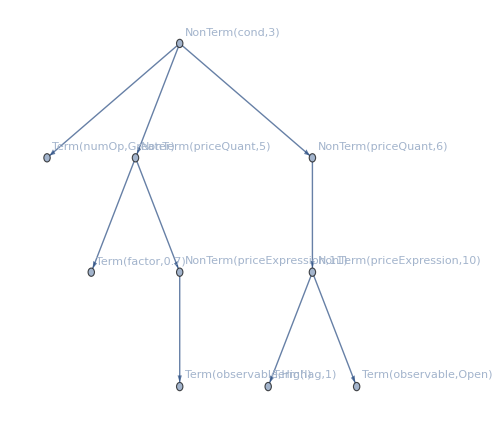
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Greater],3→NonTerm[priceQuant,5],4→Term[factor,0.7],5→NonTerm[priceExpression,11],6→Term[observable,High],7→NonTerm[priceQuant,6],8→NonTerm[priceExpression,10],9→Term[lag,1],10→Term[observable,Open]}}

Greater[Times[0.7,"High"],Prev["Open",1]]

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet,100]
SynthesizeTree[g,l,grammar] // FullForm
```

```mathematica
GenerateInitialPopulation[size_,maxDepth_,trainingDates_,stocks_,transactionCost_,livingExpenses_,bloatControl_]:=Block[{seeds,populationGenomes,population},
populationGenomes = Table[GenerateRandomFunction[grammar,terminalSet,maxDepth],size];
population = Map[<|"Genome"->#,"Score"->0|>&,populationGenomes];

EvaluatePopulation[population,trainingDates,stocks,transactionCost,livingExpenses,bloatControl]
];
```

```mathematica
population = GenerateInitialPopulation[10,100,trainingDates,0.0025,0.0,0.0];
```

## Selection

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]];
```

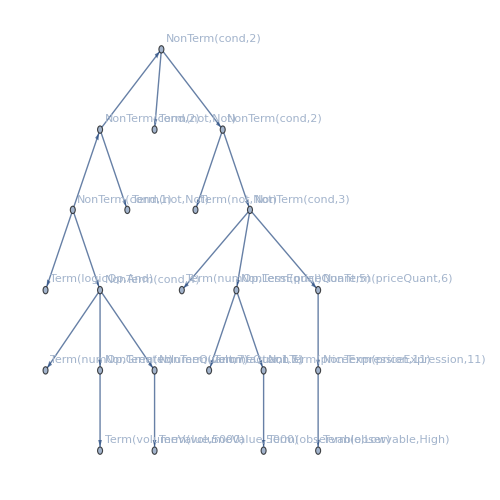
{<|Genome→{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,2],4→Term[not,Not],5→NonTerm[cond,2],6→Term[not,Not],7→NonTerm[cond,2],8→Term[not,Not],9→NonTerm[cond,3],10→Term[numOp,LessEqual],11→NonTerm[priceQuant,5],12→Term[factor,1.5],13→NonTerm[priceExpression,11],14→Term[observable,Low],15→NonTerm[priceQuant,6],16→NonTerm[priceExpression,11],17→Term[observable,High],18→NonTerm[cond,4],19→Term[numOp,Greater],20→NonTerm[volumeQuant,7],21→Term[volumeValue,5000],22→NonTerm[volumeQuant,7],23→Term[volumeValue,5000]}},Score→0.|>}

```mathematica
selected = ProportionateRankedSelection[population,1]
```

## Main algorithm

```mathematica
Generation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,stocks_,transactionCost_,livingExpenses_,bloatControl_]:=Block[{healthyChildren,evaluated,fittest,newGeneration,mutated,childrenPerCouple,elite,sortedWithElite,newBlood,evaluatedElite,expressions,badExpressions},
fittest = ProportionateRankedSelection[population,survivors];
childrenPerCouple = (2 Length[population])/survivors;
newGeneration = PopulationCrossover[fittest,childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb,terminalSet];

expressions = Map[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar]&,mutated];
badExpressions = Position[expressions,True|False];
healthyChildren = Delete[mutated,badExpressions];

evaluated = SortBy[EvaluatePopulation[healthyChildren,trainingDates,stocks,transactionCost,livingExpenses,bloatControl],Key["Score"]];
elite = Take[Reverse@SortBy[population,Key["Score"]],elitism+Length[badExpressions]];
evaluatedElite = EvaluatePopulation[elite,trainingDates,stocks,transactionCost,livingExpenses,bloatControl];
sortedWithElite = Reverse@SortBy[Join[evaluatedElite,Drop[evaluated,elitism]],Key["Score"]];

If[newBloodIndividuals ≠ 0,
newBlood = GenerateInitialPopulation[newBloodIndividuals+Length[badExpressions],100,trainingDates,stocks,transactionCost,livingExpenses,bloatControl],
newBlood = {}
];

Reverse@SortBy[Join[Drop[sortedWithElite,-newBloodIndividuals-Length[badExpressions]],newBlood],Key["Score"]]
];
```

### Non-interactive evolution

```mathematica
EvolvePopulation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,stocks_,transactionCost_,livingExpenses_,bloatControl_,generations_]:=
ProgressNestList[
Generation[#,survivors,mutationProb,elitism,newBloodIndividuals,trainingDates,stocks,transactionCost,livingExpenses,bloatControl]&,
population,generations,
"Label"->"Generation"
];
```

```mathematica
population = GenerateInitialPopulation[200,100,trainingDates,0.0025,0.005];
```

```mathematica
evolved = EvolvePopulation[population,50,0.5,2,trainingDates,0.0025,0.005,30];
```

```mathematica
evaluatedOnValidation = ProgressTable[Reverse@SortBy[EvaluatePopulation[evolved[[i]][[All,"Genome"]],validationDates,0.0025],Key["Score"]],{i,1,Length[evolved]}];
```

```mathematica
trainingScoreVsIter = Table[{k,Mean[evolved[[k]][[All,"Score"]]]},{k,1,Length[evolved]}];
validationScoreVsIter = Table[{k,Mean[evaluatedOnValidation[[k]][[All,"Score"]]]},{k,1,Length[evaluatedOnValidation]}];

ListLinePlot[
{trainingScoreVsIter,validationScoreVsIter},
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLegends->{"Training set","Validation set"}
]
```

### Interactive evolution

```mathematica
GetSeconds[time_] := IntegerString[Round[Mod[time, 60]], 10, 2];
GetMinutes[time_]:= IntegerString[Mod[Floor[time/60], 60], 10, 2];
GetHours[time_] := IntegerString[Floor[time/3600], 10, 2];
ClockFormat[time_] := StringJoin[GetHours[time], ":", GetMinutes[time], ":", GetSeconds[time]];

ProgressEvolveIndicator[indexProgress_,totalSize_,startTime_,fittestIndPlot_,averageIndPlot_,worstIndPlot_,scorePlot_,scoresHistogram_,popSize_]:=Block[{progressString,remainingTime,remainingTimeString,indicator,ellapsedTimeString},
progressString = Row[{Style["Progress: ",Bold],ToString[indexProgress],"/",ToString[totalSize]}];
ellapsedTimeString = Row[{Style["Ellapsed time: ",Bold],ClockFormat[AbsoluteTime[]-startTime]}];

If[indexProgress ≠ 0,
remainingTime = (AbsoluteTime[]-startTime)/indexProgress(totalSize-indexProgress);
remainingTimeString = Row[{Style["Remaining: ",Bold],ClockFormat[remainingTime]}];
,
remainingTimeString = Row[{Style["Remaining: ", Bold],"Unknown"}];
];

indicator = Panel[
Column[
{
Style["Generation",Bold],
ProgressIndicator[indexProgress,{1,totalSize}],
progressString,
ellapsedTimeString,
remainingTimeString,
Row[{Style["Population size: ", Bold],popSize}],
Style["Scores: ", Bold],
Row[{scorePlot,scoresHistogram}],
Style["Fittest individuals: ", Bold],
fittestIndPlot,
Style["Average individuals: ", Bold],
averageIndPlot,
Style["Worst individuals: ", Bold],
worstIndPlot
}
]
];

Return[indicator];
];
ProgressEvolvePopulation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,stocks_,transactionCost_,livingExpenses_,bloatControl_,generations_]:=Block[{scorePlot,fittestIndPlot,currentGeneration = population,startTime = AbsoluteTime[],indexProgress = 0,scoreVsK={},allGenerations={population},scoresHistogram,averagePos,averageIndPlot,worstIndPlot},
Monitor[
Do[
AppendTo[scoreVsK,Max[currentGeneration[[All,"Score"]]]];
scorePlot = ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Best Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"Score",
Frame->True,
ImageSize->500,
PlotRange->All
];
fittestIndPlot = Row@Map[TreeForm[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar],ImageSize->400,PlotLabel->#["Score"]]&,Take[currentGeneration,3]];
averagePos = Length[currentGeneration]/2;
averageIndPlot = Row@Map[TreeForm[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar],ImageSize->400,PlotLabel->#["Score"]]&,Take[currentGeneration,{averagePos-1,averagePos+1}]];
worstIndPlot = Row@Map[TreeForm[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar],ImageSize->400,PlotLabel->#["Score"]]&,Take[currentGeneration,-3]];
scoresHistogram = Histogram[
Select[currentGeneration[[All,"Score"]],-0.1<#<0.1&],20,
PlotTheme->"Monochrome",
FrameLabel->{Style["Score",15], Style["Frequency",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{0},{}},
PlotLabel->"Score",
Frame->True,
ImageSize->500,
PlotRange->All
];

currentGeneration = Generation[currentGeneration,survivors,mutationProb,elitism,newBloodIndividuals,trainingDates,stocks,transactionCost,livingExpenses,bloatControl];
AppendTo[allGenerations,currentGeneration];
indexProgress++;
,generations
],
ProgressEvolveIndicator[indexProgress,generations,startTime,fittestIndPlot,averageIndPlot,worstIndPlot,scorePlot,scoresHistogram,Length[currentGeneration]]
];

Return[allGenerations];
];
```

```mathematica
¨
```

## Experiments

```mathematica
TestStrategy[strategyFunc_,dayIndex_,stocks_]:=Map[StrategyReturn[strategyFunc,stockDatabase[[dayIndex,#]],0.0]&,stocks];
```

### Results on soda stocks

```mathematica
bloatControl = 0.0;
transactionCost = 0.0;
livingExpenses = 0.001;
useDates = Take[trainingDates,2];
useStocks = {"AC.MX","KOFUBL.MX"};
population = GenerateInitialPopulation[200,100,useDates,useStocks,transactionCost,livingExpenses,bloatControl];
```

```mathematica
evolved = ProgressEvolvePopulation[population,100,0.3,3,10,useDates,useStocks,transactionCost,livingExpenses,bloatControl,50];
```

```mathematica
{bestg,bestl} = evolved[[-1]][[1]]["Genome"];
SynthesizeTree[bestg,bestl,grammar]
```

!(!(1.5 Low≤1.5 Prev[Low,20]||Volume>Prev[Volume,1])||Volume>1000)

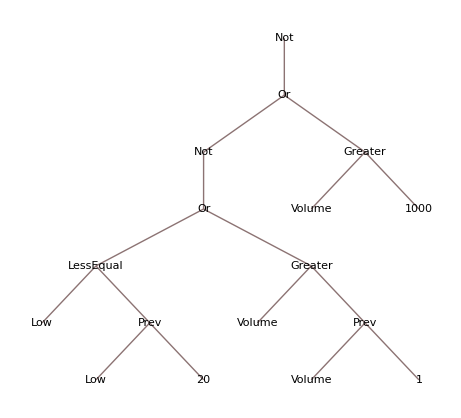

```mathematica
TreeForm[!(!( "Low"≤Prev["Low",20]||"Volume">Prev["Volume",1])||"Volume">1000)]
```

```mathematica
results = ProgressTable[TestStrategy[!(!( "Low"≤Prev["Low",20]||"Volume">Prev["Volume",1])||"Volume">1000),i,useStocks],{i,1,Length[dates]-2}];
```

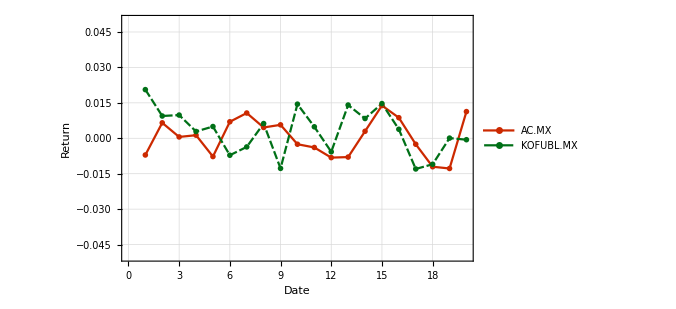

```mathematica
ListLinePlot[
Transpose[results],PlotRange->{{0,20},{-0.05,0.05}},
PlotLegends->useStocks,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",15], Style["Return",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.44, 0.09],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
]
```

```mathematica
Total[Flatten[results]]
```

0.0688355

### Results on airlines stocks

```mathematica
bloatControl = 0.0;
transactionCost = 0.0;
livingExpenses = 0.001;
useDates = Take[trainingDates,2];
useStocks = {"ASURB.MX","GAPB.MX","OMAB.MX"};
population = GenerateInitialPopulation[200,100,useDates,useStocks,transactionCost,livingExpenses,bloatControl];
```

```mathematica
evolved = ProgressEvolvePopulation[population,100,0.3,3,10,useDates,useStocks,transactionCost,livingExpenses,bloatControl,50];
```

```mathematica
{bestg,bestl} = evolved[[-1]][[1]]["Genome"];
SynthesizeTree[bestg,bestl,grammar]
```

1.5 SMA[Low,20]>0.7 Prev[Low,1]&&Low>Prev[Close,1]

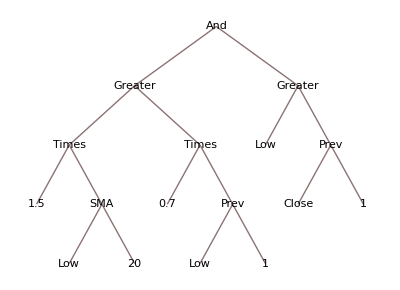

```mathematica
TreeForm[1.5 SMA["Low",20]>0.7 Prev["Low",1]&&"Low">Prev["Close",1]]
```

```mathematica
results = ProgressTable[TestStrategy[1.5 SMA["Low",20]>0.7 Prev["Low",1]&&"Low">Prev["Close",1],i,useStocks],{i,1,Length[dates]-2}];
```

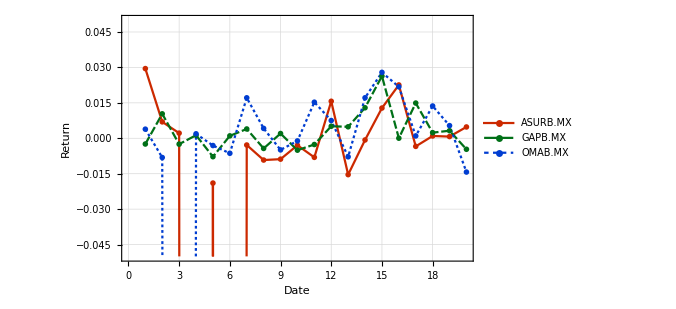

```mathematica
ListLinePlot[
Transpose[results],PlotRange->{{0,20},{-0.05,0.05}},
PlotLegends->useStocks,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",15], Style["Return",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.8, 0.16, 0.],RGBColor[0., 0.44, 0.09],RGBColor[0., 0.24, 0.8200000000000001]},
Frame->True,
ImageSize->500
]
```

```mathematica
Total[Flatten[results]]
```

-16.6324